```mathematica
"ϕ==> Rotate"
"θ==> Tilt"
"ψ==>Twist"
"χ_(i, j, k)^(2)==>Laboratory Coordination, λ(x,y,z)"
"χ_(l, m, n)^(2)==>Molecular Coordination, η(a,b,c)"
```

```mathematica
"From C2V Character Table"
```

```mathematica
"β_(a, a, c)==A_1 ⊗ A_1==A_1,   Symmetric"
"β_(a, c, a)==B_1 ⊗ B_1==A_1,   Asymmetric"
"β_(b, b, c)==A_1 ⊗ A_1==A_1,   Symmetric"
"β_(b, c, b)==B_2 ⊗ B_2==A_1,   Asymmetric"
"β_(c, a, a)==B_1 ⊗ B_1==A_1,   Asymmetric"
"β_(c, b, b)==B_2 ⊗ B_2==A_1,   Asymmetric"
"β_(c, c, c)==A_1 ⊗ A_1==A_1,   Symmetric"
```

```mathematica
x=a=1
y=b=2
z=c=3
```

1

2

3

```mathematica
"Non-zero Microscopic Hyperpolarizability"
```

```mathematica
"Symmetric"
Subscript[β, a,a,c]
Subscript[β, b,b,c]
Subscript[β, c,c,c]
"Asymmetric, B_1"
Subscript[β, c,a,a]=Subscript[β, a,c,a]
"Asymmetric, B_2"
Subscript[β, c,b,b]=Subscript[β, b,c,b]
```

Symmetric

β_(1,1,3)

β_(2,2,3)

β_(3,3,3)

Asymmetric

β_(1,3,1)

β_(2,3,2)

```mathematica
"Zero Microscopic Hyperpolarizability"
```

```mathematica
Subscript[β, a,a,a]=Subscript[β, a,a,b]=Subscript[β, a,b,a]=Subscript[β, a,b,b]=Subscript[β, a,b,c]=Subscript[β, a,c,b]=Subscript[β, a,c,c]=0
Subscript[β, b,a,a]=Subscript[β, b,a,b]=Subscript[β, b,a,c]=Subscript[β, b,b,a]=Subscript[β, b,b,b]=Subscript[β, b,c,a]=Subscript[β, b,c,c]=0
Subscript[β, c,a,b]=Subscript[β, c,a,c]=Subscript[β, c,b,a]=Subscript[β, c,b,c]=Subscript[β, c,c,a]=Subscript[β, c,c,b]=0
```

0

0

0

```mathematica
"Euler Transformation Matrix"
```

```mathematica
ℝ=({{Cos[ψ]Cos[ϕ]-Cos[θ]Sin[ϕ]Sin[ψ], -Sin[ψ]Cos[ϕ]-Cos[θ]Sin[ϕ]Cos[ψ], Sin[θ]Sin[ϕ]}, {Cos[ψ]Sin[ϕ]+Cos[θ]Cos[ϕ]Sin[ψ], -Sin[ψ]Sin[ϕ]+Cos[θ]Cos[ϕ]Cos[ψ], -Sin[θ]Cos[ϕ]}, {Sin[θ]Sin[ψ], Sin[θ]Cos[ψ], Cos[θ]}})
```

{{Cos[ϕ] Cos[ψ]-Cos[θ] Sin[ϕ] Sin[ψ],-Cos[θ] Cos[ψ] Sin[ϕ]-Cos[ϕ] Sin[ψ],Sin[θ] Sin[ϕ]},{Cos[ψ] Sin[ϕ]+Cos[θ] Cos[ϕ] Sin[ψ],Cos[θ] Cos[ϕ] Cos[ψ]-Sin[ϕ] Sin[ψ],-Cos[ϕ] Sin[θ]},{Sin[θ] Sin[ψ],Cos[ψ] Sin[θ],Cos[θ]}}

```mathematica
"For SSP"
```

```mathematica
Subscript[χ, i, j, k]=∑_(l=a)^c ∑_(m=a)^c ∑_(n=a)^c   ℝ[[i,l]] ℝ[[j,m]] ℝ[[k,n]] Subscript[β, l ,m ,n]/.{i->y,j->y,k->z}
```

Part::pspec: Part specification i is neither an integer nor a list of integers.

Part::pspec: Part specification j is neither an integer nor a list of integers.

Part::pspec: Part specification k is neither an integer nor a list of integers.

General::stop: Further output of Part will be suppressed during this calculation.

Cos[θ] (Cos[ψ] Sin[ϕ]+Cos[θ] Cos[ϕ] Sin[ψ])^2 β_(1,1,3)-2 Cos[ϕ] Sin[θ]^2 Sin[ψ] (Cos[ψ] Sin[ϕ]+Cos[θ] Cos[ϕ] Sin[ψ]) β_(1,3,1)+Cos[θ] (Cos[θ] Cos[ϕ] Cos[ψ]-Sin[ϕ] Sin[ψ])^2 β_(2,2,3)-2 Cos[ϕ] Cos[ψ] Sin[θ]^2 (Cos[θ] Cos[ϕ] Cos[ψ]-Sin[ϕ] Sin[ψ]) β_(2,3,2)+Cos[θ] Cos[ϕ]^2 Sin[θ]^2 β_(3,3,3)

```mathematica
"SSP Symmetric Stretching-->β_(a, a, c) , β_(b, b, c) , β_(c, c, c)"
```

```mathematica
Subscript[χ, y,y,z]^((2)ss)=
Expand[Cos[θ] (Cos[ψ] Sin[ϕ]+Cos[θ] Cos[ϕ] Sin[ψ])^2 Subscript[β, a,a,c]+Cos[θ] (Cos[θ] Cos[ϕ] Cos[ψ]-Sin[ϕ] Sin[ψ])^2 Subscript[β, b,b,c]+Cos[θ] Cos[ϕ]^2 Sin[θ]^2 Subscript[β, c,c,c]]

=Cos[θ] Cos[ψ]^2 Sin[ϕ]^2 Subscript[β, a,a,c]+2 Cos[θ]^2 Cos[ϕ] Cos[ψ] Sin[ϕ] Sin[ψ] Subscript[β, a,a,c]+Cos[θ]^3 Cos[ϕ]^2 Sin[ψ]^2 Subscript[β, a,a,c]+Cos[θ]^3 Cos[ϕ]^2 Cos[ψ]^2 Subscript[β, b,b,c]-2 Cos[θ]^2 Cos[ϕ] Cos[ψ] Sin[ϕ] Sin[ψ] Subscript[β, b,b,c]+Cos[θ] Sin[ϕ]^2 Sin[ψ]^2 Subscript[β, b,b,c]+Cos[θ] Cos[ϕ]^2 Sin[θ]^2 Subscript[β, c,c,c]

=Cos[θ] Cos[ψ]^2 Sin[ϕ]^2 Subscript[β, a,a,c]+2 Cos[θ]^2 Cos[ϕ] Cos[ψ] Sin[ϕ] Sin[ψ] Subscript[β, a,a,c]+Cos[θ]^3 Cos[ϕ]^2 Sin[ψ]^2 Subscript[β, a,a,c]+Cos[θ]^3 Cos[ϕ]^2 Cos[ψ]^2 Subscript[β, b,b,c]-2 Cos[θ]^2 Cos[ϕ] Cos[ψ] Sin[ϕ] Sin[ψ] Subscript[β, b,b,c]+Cos[θ] Sin[ϕ]^2 Sin[ψ]^2 Subscript[β, b,b,c]+Cos[θ] Cos[ϕ]^2 Subscript[β, c,c,c]-Cos[θ]^3 Cos[ϕ]^2 Subscript[β, c,c,c]

=( Sin[ϕ]^2 Cos[ψ]^2 Subscript[β, a,a,c]+Sin[ϕ]^2 Sin[ψ]^2 Subscript[β, b,b,c]+Cos[ϕ]^2 Subscript[β, c,c,c])Cos[θ]+2(Subscript[β, a,a,c]- Subscript[β, b,b,c])Cos[θ]^2 Cos[ϕ] Cos[ψ] Sin[ϕ] Sin[ψ]+(Cos[ϕ]^2 Sin[ψ]^2 Subscript[β, a,a,c]+Cos[ϕ]^2 Cos[ψ]^2 Subscript[β, b,b,c]-Cos[ϕ]^2 Subscript[β, c,c,c])Cos[θ]^3
```

```mathematica
"Average Over Orientation (ϕ)-Non Free Rotation of C2V Group"
```

```mathematica
Subscript[Ν, s]/(2π)Cos[θ](∫_0^(2π) (( Sin[ϕ]^2 Cos[ψ]^2 Subscript[β, a,a,c]+Sin[ϕ]^2 Sin[ψ]^2 Subscript[β, b,b,c]+Cos[ϕ]^2 Subscript[β, c,c,c]))ⅆϕ)+Subscript[Ν, s]/(2π)2 Cos[θ]^2 (∫_0^(2π) (Cos[ϕ] Cos[ψ] Sin[ϕ] Sin[ψ]( Subscript[β, a,a,c]- Subscript[β, b,b,c]))ⅆϕ)+Subscript[Ν, s]/(2π)Cos[θ]^3(∫_0^(2π) (( Cos[ϕ]^2 Sin[ψ]^2 Subscript[β, a,a,c]+Cos[ϕ]^2 Cos[ψ]^2 Subscript[β, b,b,c]-Cos[ϕ]^2 Subscript[β, c,c,c]))ⅆϕ)

=1/2 Cos[θ]^3 Subscript[Ν, s] (Sin[ψ]^2 Subscript[β, a,a,c]+Cos[ψ]^2 Subscript[β, b,b,c]-Subscript[β, c,c,c])+1/2 Cos[θ] Subscript[Ν, s] (Cos[ψ]^2 Subscript[β, a,a,c]+Sin[ψ]^2 Subscript[β, b,b,c]+Subscript[β, c,c,c])
```

```mathematica
Subscript[χ, y,y,z]^((2)ss)=1/2  Subscript[Ν, s] (Cos[ψ]^2 Subscript[β, a,a,c]+Sin[ψ]^2 Subscript[β, b,b,c]+Subscript[β, c,c,c])Cos[θ]+1/2  Subscript[Ν, s] (Sin[ψ]^2 Subscript[β, a,a,c]+Cos[ψ]^2 Subscript[β, b,b,c]-Subscript[β, c,c,c])Cos[θ]^3
```

```mathematica
"Plot"
```

```mathematica
Subscript[Ν, s]=1
Subscript[β, a,a,c]=1
Subscript[β, b,b,c]=1
Subscript[β, c,c,c]=1
```

1

1

1

«1 more identical outputs»

```mathematica
Plot3D[1/2  Subscript[Ν, s] (Cos[ψ]^2 Subscript[β, a,a,c]+Sin[ψ]^2 Subscript[β, b,b,c]+Subscript[β, c,c,c])Cos[θ]+1/2  Subscript[Ν, s] (Sin[ψ]^2 Subscript[β, a,a,c]+Cos[ψ]^2 Subscript[β, b,b,c]-Subscript[β, c,c,c])Cos[θ]^3,{θ,0Degree, 180 Degree},{ψ,0Degree, 180 Degree},AxesLabel->{θ,ψ}]
```

-Graphics3D-

```mathematica
"Average Over Orientation (ϕ,ψ)-Free Rotation of C2V Group"
```

```mathematica
1/(2π)(∫_0^(2π) (1/2  Subscript[Ν, s] (Cos[ψ]^2 Subscript[β, a,a,c]+Sin[ψ]^2 Subscript[β, b,b,c]+Subscript[β, c,c,c])Cos[θ])ⅆψ)+1/(2π)(∫_0^(2π) (1/2    Subscript[Ν, s] (Sin[ψ]^2 Subscript[β, a,a,c]+Cos[ψ]^2 Subscript[β, b,b,c]-Subscript[β, c,c,c])Cos[θ]^3)ⅆψ)

=1/4 Cos[θ]^3 Subscript[Ν, s] (Subscript[β, a,a,c]+Subscript[β, b,b,c]-2 Subscript[β, c,c,c])+1/4 Cos[θ] Subscript[Ν, s] (Subscript[β, a,a,c]+Subscript[β, b,b,c]+2 Subscript[β, c,c,c])
```

```mathematica
Subscript[χ, y,y,z]^((2)ss)=1/4  Subscript[Ν, s] (Subscript[β, a,a,c]+Subscript[β, b,b,c]+2 Subscript[β, c,c,c])Cos[θ]+1/4  Subscript[Ν, s] (Subscript[β, a,a,c]+Subscript[β, b,b,c]-2 Subscript[β, c,c,c])Cos[θ]^3
```

```mathematica
"Plot"
```

```mathematica
Subscript[Ν, s]=1
Subscript[β, a,a,c]=1
Subscript[β, b,b,c]=1
Subscript[β, c,c,c]=1
```

1

1

1

«1 more identical outputs»

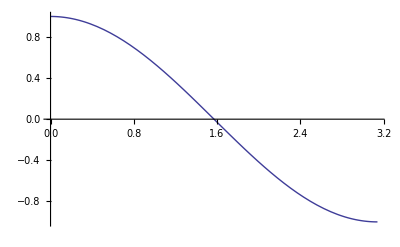

```mathematica
Plot[1/4  Subscript[Ν, s] (Subscript[β, a,a,c]+Subscript[β, b,b,c]+2 Subscript[β, c,c,c])Cos[θ]+1/4  Subscript[Ν, s] (Subscript[β, a,a,c]+Subscript[β, b,b,c]-2 Subscript[β, c,c,c])Cos[θ]^3,{θ,0Degree, 180 Degree}]
```

```mathematica
"SSP, B_1 Asymmetric Stretching-->β_(a, c, a)"
```

```mathematica
Subscript[χ, y,y,z]^((2)as,Subscript[B, 1])=
Expand[-2 Cos[ϕ] Sin[θ]^2 Sin[ψ] (Cos[ψ] Sin[ϕ]+Cos[θ] Cos[ϕ] Sin[ψ])Subscript[β, a,c,a]]

=-2 Cos[ϕ] Cos[ψ] Sin[θ]^2 Sin[ϕ] Sin[ψ] Subscript[β, a,c,a]-2 Cos[θ] Cos[ϕ]^2 Sin[θ]^2 Sin[ψ]^2 Subscript[β, a,c,a]
```

```mathematica
"Average Over Orientation (ϕ)-Non Free Rotation of C2V Group"
```

```mathematica
Subscript[Ν, s]/(2π)(∫_0^(2π) (-2 Cos[ϕ] Cos[ψ] Sin[θ]^2 Sin[ϕ] Sin[ψ] Subscript[β, a,c,a]-2 Cos[θ] Cos[ϕ]^2 Sin[θ]^2 Sin[ψ]^2 Subscript[β, a,c,a])ⅆϕ)

=-Cos[θ] Sin[θ]^2 Sin[ψ]^2 Subscript[Ν, s] Subscript[β, a,c,a]
```

```mathematica
Subscript[χ, y,y,z]^((2)as,Subscript[B, 1])=-Subscript[Ν, s] Subscript[β, a,c,a] Sin[ψ]^2(Cos[θ]- Cos[θ]^3)
```

```mathematica
"Plot"
```

```mathematica
Subscript[Ν, s]=1
Subscript[β, a,c,a]=1
```

1

1

```mathematica
Plot3D[-Subscript[Ν, s] Subscript[β, a,c,a] Sin[ψ]^2(Cos[θ]- Cos[θ]^3),{θ,0 Degree,190 Degree},{ψ,0 Degree,180 Degree},AxesLabel->{θ,ψ}]
```

-Graphics3D-

```mathematica
"Average Over Orientation (ϕ,ψ)-Free Rotation of C2V Group"
```

```mathematica
1/(2π)(∫_0^(2π) (-Subscript[Ν, s] Subscript[β, a,c,a] Sin[ψ]^2(Cos[θ]- Cos[θ]^3))ⅆψ)

=-1/2 Subscript[Ν, s] Cos[θ] Sin[θ]^2 Subscript[β, a,c,a]
```

```mathematica
Subscript[χ, y,y,z]^((2)as,Subscript[B, 1])=-1/2 Subscript[Ν, s] Subscript[β, a,c,a](Cos[θ]- Cos[θ]^3)
```

```mathematica
"Plot"
```

```mathematica
Subscript[Ν, s]=1
Subscript[β, a,c,a]=1
```

1

1

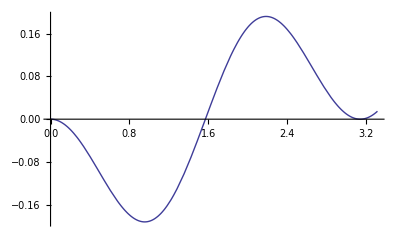

```mathematica
Plot[-1/2 Subscript[Ν, s] Subscript[β, a,c,a](Cos[θ]- Cos[θ]^3),{θ,0 Degree,190 Degree}]
```

```mathematica
"SSP, B_2 Asymmetric Stretching-->β_(b, c, b)"
```

```mathematica
Subscript[χ, y,y,z]^((2)as,Subscript[B, 2])=
Expand[-2 Cos[ϕ] Cos[ψ] Sin[θ]^2 (Cos[θ] Cos[ϕ] Cos[ψ]-Sin[ϕ] Sin[ψ]) Subscript[β, b,c,b]]

=-2 Cos[θ] Cos[ϕ]^2 Cos[ψ]^2 Sin[θ]^2 Subscript[β, b,c,b]+2 Cos[ϕ] Cos[ψ] Sin[θ]^2 Sin[ϕ] Sin[ψ] Subscript[β, b,c,b]
```

```mathematica
"Average Over Orientation (ϕ)-Non Free Rotation of C2V Group"
```

```mathematica
Subscript[Ν, s]/(2π)(∫_0^(2π) (-2 Cos[θ] Cos[ϕ]^2 Cos[ψ]^2 Sin[θ]^2 Subscript[β, b,c,b]+2 Cos[ϕ] Cos[ψ] Sin[θ]^2 Sin[ϕ] Sin[ψ] Subscript[β, b,c,b])ⅆϕ)

=-Cos[θ] Cos[ψ]^2 Sin[θ]^2 Subscript[Ν, s] Subscript[β, b,c,b]
```

```mathematica
Subscript[χ, y,y,z]^((2)as,Subscript[B, 2])=-Subscript[Ν, s] Subscript[β, b,c,b] Sin[ψ]^2(Cos[θ]- Cos[θ]^3)
```

```mathematica
"Plot"
```

```mathematica
Subscript[Ν, s]=1
Subscript[β, b,c,b]=1
```

1

1

```mathematica
Plot3D[-Subscript[Ν, s] Subscript[β, b,c,b] Sin[ψ]^2(Cos[θ]- Cos[θ]^3),{θ,0Degree, 180 Degree},{ψ,0Degree, 180 Degree},AxesLabel->{θ,ψ}]
```

-Graphics3D-

```mathematica
"Average Over Orientation (ϕ,ψ)-Free Rotation of C2V Group"
```

```mathematica
1/(2π)(∫_0^(2π) (-Subscript[Ν, s] Subscript[β, b,c,b] Sin[ψ]^2(Cos[θ]- Cos[θ]^3))ⅆψ)

=-1/2 Subscript[Ν, s] Cos[θ] Sin[θ]^2 Subscript[β, b,c,b]
```

-1/2 Cos[θ] Sin[θ]^2 β_(b,c,b)

```mathematica
Subscript[χ, y,y,z]^((2)as,Subscript[B, 2])=-1/2 Subscript[Ν, s] Subscript[β, b,c,b](Cos[θ]- Cos[θ]^3)
```

```mathematica
"Plot"
```

```mathematica
Subscript[Ν, s]=1
Subscript[β, b,c,b]=1
```

1

1

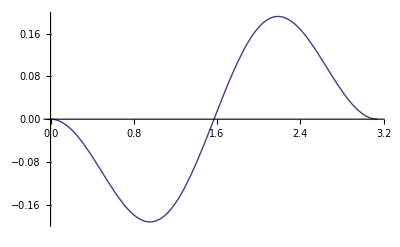

```mathematica
Plot[-1/2 Subscript[Ν, s] Subscript[β, b,c,b](Cos[θ]- Cos[θ]^3),{θ,0Degree, 180 Degree}]
```